## Cvičenie 1 - Úvod do programového systému Mathematica

### Mathematica ako vedecká kalkulačka

#### Bunka, vstup a výstup

Do vstupnej bunky zadáte požiadavku na výpočet a pomocou klávesy Enter na numerickej klávesnici, alebo kombinácie kláves Shift + Enter odošlete bunku na spracovanie do výpočtového jadra Mathematice. Vyskúšajte si to.

```mathematica
2+3
```

5

Vyskúšajte ako fungujú nasledovné príkazy

#### Čísla - celé čísla, reálne čísla

Zadať môžete ľubovoľné číslo, ale keďže zadaním čísla nepožadujete realizovať žiaden výpočet, výstup je rovnaký ako vstupná bunka. 

V nasledovných príkladoch vidíte ukážku zadania kladného, záporného, aj reálneho čísla.

```mathematica
2
```

2

```mathematica
-2
```

-2

```mathematica
2.3
```

2.3

#### Zlomky

Zlomky možete zadávať priamym zápisom pomocou znaku z klávesnice :  / , alebo aj ako predefinovaný vstup z palety  BasicMathInput -  □/□
Ak radi používate klávesové skratky, môžete používať kombináciu: čitateľ Ctrl / .

Vyskúšajte si zadávanie zlomkov.

```mathematica
2/3
```

2/3

```mathematica
2/3
```

2/3

#### Komplexné čísla

Komplexné čísla sú tvorené reálnou a imaginárnou časťou. Na zápis ⅈ používame Mathematica konštantu I

```mathematica
3+4I
```

3+4 ⅈ

#### Konštanty

Najčastejšie budeme používať nasledovné konštanty
	π , Pi 			Ludolfovo číslo
	E			základ prirodzeného logaritmu
	Infinity			∞
	I			komlpexné ⅈ
	Degree, °		stupne pri zadávaní veľkosti uhlov
Vyskúšajte si prácu s konštantami a výpočet ich numerickej hodnoty.

```mathematica
E//N
```

2.71828

```mathematica
N[E]
```

2.71828

```mathematica
N[E,10]
```

2.718281828

```mathematica
N[E,100]
```

2.718281828459045235360287471352662497757247093699959574966967627724076630353547594571382178525166427

```mathematica
Pi
```

π

```mathematica
Pi//N
```

3.14159

```mathematica
π
```

π

```mathematica
Infinity
```

∞

```mathematica
-Infinity
```

-∞

#### Grécke písmená

Vo výpočtoch môžete používať aj grécke písmená rovnako, ako obyčajné znaky našej abecedy. Zadať ich môžete pomocou paliet "BasicMathInput" alebo "BasicTypesetting", alebo pomocou klávesových skratiek: Esc písmeno Esc.
Vyskúšajte si zadanie písmen gréckej abecedy - α, ρ, σ, π, μ

```mathematica
α
```

α

```mathematica
μ
```

μ

#### Aritmetické operácie

Rovnako ako pri práci s kalkulačkou budete používať základné matematické operácie - sčítanie a odčítanie. Používame rovnaké symboly ako pri práci s kalkulačkou: +, -
Zrealizujte niekoľko jednoduchých výpočtov s reálnymi aj s komplexnými číslami.

```mathematica
2+3
```

5

```mathematica
2-3.2
```

-1.2

```mathematica
3+2I-2
```

1+2 ⅈ

Pre násobenie používame znak * alebo  medzeru. Používanie medzier (vysvetlenie, čo je povolené) pri násobení je podrobne popísané v kapitole "Šesť pravidiel". Prečítajte si ju a potom si vyskúšajte zrealizovať niekoľko jednoduchých úloh.

```mathematica
2*3
```

6

```mathematica
(3+2I)*(2-I)
```

8+ⅈ

Rovnako ako pri práci s kalkulačkou budete používať základné matematické operácie - sčítanie a odčítanie. Používame rovnaké symboly ako pri práci s kalkulačkou: +, -
Zrealizujte niekoľko jednoduchých výpočtov s reálnymi aj s komplexnými číslami.

POZOR: pri práci s paletou nájdete na nej dva znaky, ktoré veľmi pripomínajú znak násobenia. Prvý znak je skutočne znakom násobenia, druhý je ale určený pre výpočet vektorového súčinu dvoch vektorov. Nezamieňajte si ich!

-Graphics-

```mathematica
2×3
```

6

Ďalšou operáciou je operácia delenia. Pri delení používame znak:  / . Ako sme spomínali na prednáške, Mathematica sa snaží dať vždy presný výsledok. Ak je to možné, tak výsledok poskytne v tvare zlomku. Ak chcete získať numerickú hodnotu je potrebné použiť príkaz N[ ... ]

Vyskúšajte si použitie nasledovných variant tohto príkazu. 
		..... // N	vypíše numerický výsledok na predefinovaný počet platných číslic (obvykle 6)
		N[ ... ]		vypíše numerický výsledok na predefinovaný počet platných číslic (obvykle 6)
		N[ ... , n ] 	vypíše numerický výsledok na n  platných číslic

Vyskúšajte si vypočítať nasledovné príklady.

```mathematica
2/3
```

2/3

```mathematica
2/3//N
```

0.666667

```mathematica
N[2/3]
```

0.666667

```mathematica
N[2/3,10]
```

0.6666666667

```mathematica
N[1000/3,10]
```

333.3333333

```mathematica
(3+2I)/(2-I)
```

4/5+(7 ⅈ)/5

Ďalšou aritmetickou operáciou je umocňovanie. Používame znak ^ . Pre zadanie možeme použiť aj klávesovú skratku: Ctrl ^, alebo vstup zadať pomocou palety "BasicMathInput" □^□
Umocňovanie má najvyššiu prioritu spomedzi všetkých aritmetických operácií.

Vyskúšajte si vypočítať nasledovné príklady.

```mathematica
2^3
```

8

```mathematica
2^2
```

4

```mathematica
3^25
```

847288609443

Poslednou základnou aritmetickou operáciou s ktorou sa zoznámime je operácia odmocňovania. Odmocňovanie môžete realizovať pomocou predefinovaných funkcií, ako napríklad  Sqrt[ ...] , alebo pomocou zadania vstupu prostredníctvom palety "BasicMathInput"  
	√□		druhá odmocnina
	□^(1/□)		n-tá odmocnina
Všimnitesi, že ak je to možné Mathematica zadá vždy presný výsledok. Numerickú hodnotu výsledku môžeme získať pomocou príkazu N [ ...].

Vyskúšajte si vypočítať nasledovné príklady.

```mathematica
√5
```

√5

```mathematica
√5//N
```

2.23607

```mathematica
Sqrt[5]
```

√5

```mathematica
8^(1/3)
```

2

```mathematica
8^(1/3)
```

2

```mathematica
√-5
```

ⅈ √5

#### Priorita vykonávania aritmetických operácií

Najvyššiu prioritu pri vykonávaní aritmetických operácií má umocňovanie ( ^ ). Potom nasleduje násobenie a delenie ( *, / ) a najnižšiu prioritu má zo základných operácií má sčítanie a odčítanie. (+, -).
Ak chcete zmeniť prioritu vykonávaných operácií môžete použiť okrúhle zátvorky: ( ).
Podrobnosti si môžete prečítať v kapitole "Šesť základných pravidiel".

Vyskúšajte si vypočítať nasledovné príklady.

```mathematica
2+(3*4)
```

14

```mathematica
2+3*4
```

14

Preštudujte si nasledovné príklady. Ukazujú, ako je dôležité správne zadať príklad a rešpektovať prioritu operácií. 
	1+3/5, (1+3)/5, 1+(3/5)
	2 + 3/4 - 7, (2+3)/(4-7), (2+3)/4-7

```mathematica
1+3/5
```

8/5

```mathematica
(1+3)/5
```

4/5

```mathematica
1+(3/5)
```

8/5

```mathematica
2+3/4-7
```

-17/4

```mathematica
(2+3)/(4-7)
```

-5/3

```mathematica
(2+3)/4-7
```

-23/4

### Zabudované funkcie

Pozor!!!!! 
Každý predefinovaný príkaz, teda aj mená zabudovaných funkcií, začínajú veľkým písmenom. 
Zoznam základných predefinovaných funkcií nájdete v 1. kapitole. Preštudujte si tento zoznam a potom vypracujte nasledovné úlohy.

### Výrazy

Na zjednodušenie výrazu sa používa príkaz  //Simplify
Výraz musíte správne zadať a potom ho môžete zjednodušiť.

```mathematica
(a^3+3 a^2 b+3 a b^2+b^3)//Simplify
```

(a+b)^3

Dosadzovací operátor /. slúži na vypočítanie hodnoty výrazu. Šipku, ktorá sa nachádza v dosadzovacom operátore napíšete buď pomocou palety "Basic Math Assistant", alebo napíšete pomocou klávesnice - (mínus) a potom znamienko >. Mathematica vstup automaticky konvertuje na šipku → .

#### Príklad

V nasledovnom príklade dosaď do výrazu a * y-7 x^2 za premennú a hodnotu 1

```mathematica
a*y-7x^2/.a->1
```

-7 x^2+y

Do predchádzajúceho výstupu dosaďte za y hodnotu 2

```mathematica
%
```

-7 x^2+y

```mathematica
%/.y->2
```

2-7 x^2

Do predpredchádzajúceho výstupu dosaďte za x →x^2

```mathematica
%%/.x->x^2
```

-7 x^4+y

Zobrazte ešte raz predchádzajúci výsledok

```mathematica
%61
```

-7 x^4+y

```mathematica
Out[61]
```

-7 x^4+y

Do výstupu číslo 62 dosaďte za a →cislo

```mathematica
Out[58]/.a->cislo
```

-7 x^2+y

Do výstupu číslo 62 dosaďte za a →(t + 4 a^2)/3

```mathematica
%61/.a->(t+4a*a)/3
```

-7 x^4+y

### Kreslíme

Príkaz Plot vykreslí graf funkcie f.Štruktúra tohoto príkazu je nasledovná
	  	 Plot [ f[x] , {x, x_min, x_max]
Tento príkaz vykreslí graf funkcie f na intervale.  Interval je potrebné zvoliť rozumným spôsobom. Ako hranice intervalu musia byť zvolené konkrétne čísla, nie je prípustné ani +∞, ani -∞ . Graf kreslíme vždy len na intervale konečnej dĺžky.

Všimnite si, že tak ako všetky ostatné príkazy, aj príkaz Plot začína veľkým písmenom a jeho argument [f[x], {x, xmin, xmax] je v hranatých zátvorkách.

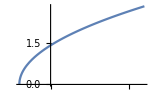

```mathematica
Plot[Sqrt[x + 2], {x, -2, 6}]
```

```mathematica
DynamicModule[{xc,dx},Manipulate[Plot[√(x+2),{x,xc-dx,xc+dx}],{{xc,2,"center"},-22,26},{{dx,4.,"zoom"},24,0.24}],DynamicModuleValues:>{}]
```

Options - voľby, sú pomocné parametre príkazov, ktoré používame len v prípade potreby.

V príkaze Plot pomocou nich môžeme meniť farbu výsledku, hrúbku čiary, rozsah pre os y - ovú, dopĺňať do obrázku popis osí a pod. Podrobnosti nájde čitate2 v Helpe (F1). Najčastejšie voľby sú: 
Option pre zmenu rozsahu intervalu kreslenia na osi y - ovej má tvar
	Plot[f[x], {x, xmin, xmax}, PlotRange -> All]
	Plot[f[x], {x, xmin, xmax}, PlotRange -> {ymin, ymax}]
Rozsah All použijeme, ak chceme nakresliť všetky hodnoty, ktoré funkcia nadobúda.
Rozsah PlotRange -> {ymin, ymax} použijeme, ak máme záujem len o vybraný interval hodnôt funkcie.

Pomocou príkazu Plot môžeme do jedného obrázka nakresliť aj grafy viac funkcií súčasne.Jeho štruktúra je potom nasledovná
	 Plot[{f[x], g[x]}, {x, xmin, xmax}]

Všimnite si, že funkcie, ktorých grafy kreslíme musia byť združené do skupiny pomocou krútených (množinových) zátvoriek f[x], g[x]. Zátvorky {, } vyjadrujú združenie objektov do jednej skupiny aj v iných prípadoch.

Nakreslené obrázky môžeme spájať pomocou príkazu Show. Príkaz Show nenakreslí žiaden obrázok, funguje len ako'' meotar'', ktorý premietne na obrazovku všetky obrázky naň položené.
Obrázky musia byť vytvorené skôr, ako ich budeme pomocou príkazu Show spájať. Jeho štruktúra je nasledovná
	Show[% cislo_obrazka, % cislo_ineho _obrazka]

### Premenné a priraďovací príkaz

Ak chceme používať nejaký výraz niekoľko krát, prípadne vytvoriť notebook s dlhodobejšou platnosťou je výhodné priradiť hodnotu výrazu nejakej premennej. Princíp priradenia je v Mathematice  rovnaký ako v ostatných programovacích jazykoch, len pravidlá priradenia sú voľnejšie tak, aby práca s premennými bola čo najpohodlnejšia.

Názvy premenných môžu byť úplne ľubovoľné, môžu obsahovať jeden, alebo viac znakov, alebo číslic. Začínať musia znakom.

MATHEMATICA je case sensitive - to znamená, že rozlišuje malé a veľké písmená. Preto premenná s názvom Pom, bude iná premenná ako premenná s názvom pom.

MATHEMATICA nedovolí pomenovať premennú rovnakým spôsobom, ako sú definované jej príkazy. To znamená, že premennú nemôžeme pomenovať Pi, pretože tieto dva znaky reprezentujú matematickú konštantu π.

Uveďme si niekoľko jednoduchých príkladov:
Do premennej a priradím hodnotu 7. Operátor priradenia je podobne ako v iných programovacích jazykov  =. Výstupom priraďovacieho príkazu je hodnota premennej. S premennou a môžeme ďalej pracovať. Spýtame sa, aká bude hodnota  a+5 .

```mathematica
a=7
```

7

```mathematica
?a
```

```mathematica
a+5
```

12

```mathematica
a^2
```

49

Ak premennú už nebudeme používať v ďalších výpočtoch je potrebné obsah pamäťového miesta, kde bola táto premenná uložená vymazať. Môžeme použiť buď príkaz 
			Clear[premenna]      		  alebo  
			Clear[premenna1, premenna2, premenna3 ...]
alebo jeho skrátený tvar
			premenna = .

### Funkcie a ich definícia

Veľmi často sa ocitáme v situácii, keď potrebujeme dlhšie pracovať s jednou funkciou - napr.potrebujeme vypočítať jej hodnotu v rôznych bodoch, nakresliť jej graf, nájsť jej priesečníky s osou x - ovou. Odvolávať sa na ňu len pomocou % je dosť nepohodlné. 
V takýchto situáciách je výhodnejšie funkciu zadefinovať. Čo to ale znamená "zadefinovať"?  Znamená to vytvoriť "priečinok", pomenovať ho menom funkcie a do vnútra uložiť predpis, ktorým je táto funkcia definovaná. Štruktúra definície funkcie vyzerá nasledovne

		f[x_] = predpis

f je názov "priečinka", premenná x je nezávisle premenná, a "predpis" nám určuje funkciu. Podčiarovník ( _ ) za nezávisle premennou je veľmi dôležitý. On nám totiž zabezpečuje, že "priečinok" bude obsahovať funkciu, a nie len obyčajné priradenie. Prirodzenou sa zdá byť otázka, čo všetko môžeme získať definíciou funkcie. Okrem jednoduchšej manipulácie s funkciou, môžeme napr.veľmi jednoducho vypočítať jej hodnotu v ľubovoľnom bode (nielen v konkrétnom čísle), ako to ukazujú nasledujúce príklady.

```mathematica
f[x_]=(x+1)/(x-4)^2
```

(1+x)/(-4+x)^2

```mathematica
?f
```

```mathematica
f[3.5]
```

18.

```mathematica
f[x+1]
```

(2+x)/(-3+x)^2

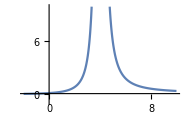

```mathematica
Plot[f[x],{x,-2,10},PlotRange->{-1,10}]
```

```mathematica
Plot[f[x],{x,-2,10},Filling->Automatic,PlotRange->{-1,10}]
```

-Graphics-

```mathematica
DynamicModule[{xc,dx},Manipulate[Plot[f[x],{x,xc-dx,xc+dx},Filling->Automatic,PlotRange->{-1,10}],{{xc,4,"center"},-32,40},{{dx,6.,"zoom"},36,0.36}],DynamicModuleValues:>{}]
```

Ak v systéme Mathematica zadefinujeme funkciu f predtým uvedeným spôsobom, vytvorený'' priečinok'' je pre našu funkciu rezervovaný až do vypnutia (Alt + F4) systému, alebo do okamihu reštartu Kernelu (možnosť Quit Kernel z MENU Evaluation). To znamená, že už žiadnu inú funkciu nemôžeme pomenovať f. Ak by sme tak spravili - dve definície by sa v'' priečinku'' bili, doplnili alebo prepísali  a získané výsledky v ďalších výpočtoch by nemuseli byť správne. podrobnejšie sa ešte tejto otázke budeme venovať neskôr.  Ak už definovanú funkciu nebudeme potrebovať, '' priečinok'' môžeme'' vyčistiť'' pomocou príkazu Clear takto
		Clear[f]

```mathematica
Clear[f]
```

Ak sa chceme systému Mathematica spýtať, čo si pamätá o globálnej premennej, alebo funkcii uloženej v pamäti, otázku sformulujeme takto:

```mathematica
?f
```

## Definícia premenných, funkcie, tabuľky, odložené priradenie

### Riešenie rovníc

Na riešenie rovníc Mathematica používa príkaz Solve. Základná štruktúra príkazu je

Solve [ rovnica , neznáma ] 			- presný výsledok.
Solve [ rovnica , neznáma ] //N		- presne vypočítané riešenie rovnice a následne je vyjadrená jeho numerická hodnota.
NSolve [ rovnica , neznáma ]			- riešenie rovnice je vypočítané numerickými metódami
FindRoot [rovnica,{neznáma, štartujúci bod}]	- riešenie rovnice Newtonovou metódou (numerická metóda), podrobnosti pozri ďalej

Všimnite si, že
	- pri zápise rovnice treba použiť operátor rovnosti == (a nie = , čo je znak operátora priradenia)
	- v príkaze je potrebné uviesť, ktorý zo symbolov v rovnici označuje neznámu.
Rovnicu musíme vždy zapísať (dve rovnitka) v tvare
		ĽavaStrana = = PravaStrana

Príkaz Solve je všeobecný. Vyrieši rovnicu, ak je možné počítať hodnoty koreňov podľa vzorcov, alebo úpravou rovnice s následným využitím vlastností inverznej funkcie. Výsledky sú vyjadrené v tvare presných čísel, ak však niektoré číslo v rovnici je v tvare desatinného čísla, aj príkaz Solve dá numerické riešenie.

Základnou množinou, v ktorej program rovnice rieši, je množina komplexných čísel C.

Vyznačenie, ktorý zo symbolov predstavuje neznámu je nutné, ak v rovnici okrem neznámej vystupujú aj parametre.

#### Príklad

Nájdite riešenie rovnice (x+3)/(x-4)=10

Riešenie:

```mathematica
Solve[(x+3)/(x-4)==10,x]
```

{{x→43/9}}

```mathematica
Solve[(x+3)/(x-4)==10,x]//N
```

{{x→4.77778}}

Dostali sme, že riešením rovnice je reálne číslo x=43/9, teda množina všetkých koreňov rovnice bude K={43/9}.

#### Príklad

Nájdite riešenie rovnice (x+4)/2-x=3-x/2.

Riešenie:

```mathematica
Solve[(x+4)/2-x==3-x/2,x]
```

{}

{}

Výstupom je { }, čo znamená, že daná rovnica v množine reálnych čísel nemá riešenie a teda K={ ∅ }.

Napíšme rovnicu do počítača a doplňujúcim príkazom Simplify ju zjednodušme.

```mathematica
(x+4)/2-x==3-x/2//Simplify
```

False

Výsledkom je odpoveď False - nepravda, ktorá potvrdzuje náš predchádzajúci výpočet pomocou príkazu Solve.

#### Príklad

Nájdite riešenie rovnice x^2-5=(x+3)(x-3)+4.

Riešenie:

```mathematica
Solve[x^2-5==(x+3)(x-3)+4,x]
```

{{}}

{{}}

Dostali sme odpoveď v tvare {{ }}, ktorý znamená, že rovnica má nekonečne veľa riešení. Aby sme našli celú množinu riešení K, podobne ako v predchádzajúcom príklade aj v tomto zjednodušme pomocou príkazu Simplify

```mathematica
x^2-5==(x+3)(x-3)+4//Simplify
```

True

Výsledkom je odpoveď True - pravda,  čo znamená že daná rovnica je identitou, čiže je splnená pre každé reálne číslo, jej riešením je množina všetkých reálnych čísel K=ℝ.

#### Príklad

Nájdite všetky riešenie rovnice x^6+2x+1=0..

Riešenie:

Zadaná rovnica je šiesteho stupňa, program nedokáže vypočítať jej presné riešenie (neexistuje explicitný vzorec pre jej výpočet). Pozrime sa, aký výsledok nám dá príkaz Solve.

```mathematica
Solve[x^6+2x+1==0,x]
```

{{x→-1},{x→Root-0.509Root[1+#1-#1^2+#1^3-#1^4+#1^5&,1]-0.5086603916420042},{x→Root-0.258-1.12 ⅈRoot[1+#1-#1^2+#1^3-#1^4+#1^5&,2]-0.2575066316165687},{x→Root-0.258+1.12 ⅈRoot[1+#1-#1^2+#1^3-#1^4+#1^5&,3]-0.2575066316165687},{x→Root1.01-0.684 ⅈRoot[1+#1-#1^2+#1^3-#1^4+#1^5&,4]1.0118368274375709},{x→Root1.01+0.684 ⅈRoot[1+#1-#1^2+#1^3-#1^4+#1^5&,5]1.0118368274375709}}

Výsledok hovorí, že jeden koreň je -1 a ostatných 5 koreňov je rovnakých ako korene polynómu 1+x-x^2+x^3-x^4+x^5, nevie ich však vypočítať.

Pozrime, aký výsledok získame pomocou príkazu NSolve

```mathematica
NSolve[x^6+2x+1==0,x]
```

{{x→-1.},{x→-0.50866},{x→-0.257507-1.11879 ⅈ},{x→-0.257507+1.11879 ⅈ},{x→1.01184-0.683959 ⅈ},{x→1.01184+0.683959 ⅈ}}

Dostali sme 6 koreňov, a teda poznáme približné hodnoty všetkých riešení rovnice.

Pomocou príkazov Solve alebo NSolve program Mathematica rieši predovšetkým algebraické rovnice. Pomocou týchto príkazov Mathematica dokáže vyriešiť aj niektoré jednoduché rovnice obsahujúce goniometrické alebo transcendentné funkcie, ale pri zložitejších typoch rovníc pomocou týchto príkazov už nemusíme nájsť všetky riešenia, alebo dokonca žiadne, aj keď existuje. Ukážeme si to na nasledujúcom príklade.

#### Príklad

Nájdite všetky riešenie rovnice e^(x-3)=ln x.

Riešenie:

Rovnica je transcendentná. Keby sme použili príkaz Solve, dostali by sme

```mathematica
Solve[Exp[x-3]==Log[x],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^(-3+x)==Log[x],x]

Vidíme, že výstup je zhodný so vstupom, týmto spôsobom program rovnicu nevie vyriešiť. Nepomôže nám ani príkaz NSolve, lebo rovnica sa nedá transformovať na algebraickú. 
Najskôr ukážeme, že riešenia naozaj existujú. Označme výrazy na ľavej strane resp. pravej strane rovnice ako hodnoty funkcií f a g, f(x)=e^(x-3) a g(x)=ln x. Hľadáme teda všetky čísla x, pre ktoré platí f(x)=g(x). Geometricky povedané, riešenia sú x. - ové súradnice priesečníkov grafov týchto funkcií. Nakreslime si grafy funkcií na intervale [0.1,5], na ktorom sú obe funkcie definované

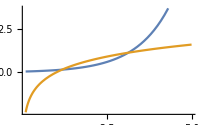

```mathematica
Plot[{Exp[x-3], Log[x]},{x,0.1,5}]
```

Na obrázku vidíme, že grafy funkcií sa pretíbajú v dvoch bodoch a z vlastností týchto elementárnych funkcií vyplýva, že viac spoločných bodov nemajú. Z obrázka môžeme odhadnúť, že jeden koreň rovnice bude v okolí bodu 1 (x_1≐ 1) a druhý bude v okolí bodu 3 (x_2≐3).

Na nájdenie koreňov tejto rovnice môžeme použiť len numerickú metódu - Newtonovu metódu.

Na nájdenie riešenia v prípadoch zložitejších rovníc môžeme použiť numerickú Newtonovu metódu, ktorá je implementovaná v príkaze FindRoot.
	
	FindRoot [ľavá strana = = pravá strana, {neznáma, štartujúci bod} ]

V tomto tvare príkaz FindRoot simuluje numerickú Newtonovu metódu (metódu dotyčníc) na nájdenie koreňa nealgebraickej rovnice. Aj keď má rovnica viac riešení, z podstaty metódy vyplýva, že príkaz FindRoot nájde vždy len jedno riešenie, najčastejšie to, ktoré je najbližšie ku štartovaciemu bodu.
Pretože v tomto predmete nemáme dostatok času na podrobné vysvetlenie, ako táto metóda funguje, sformulujeme len niektoré zásady, ktoré je potrebné dodržať pri voľbe štartovacieho bodu. Štartovací bod volíme v blízkosti koreňa (na základe grafického znázornenie funkcie) tak, aby to nebol bod maxima ani minima funkcie. Medzi zvoleným štartovacím bodom a koreňom rovnice sa nesmie nachádzať ani žiadne iné maximum ani minimum.

Z obrázka vieme, že rovnica má dva reálne korene, ktorých hodnoty sú približne 1 a 3. Na nájdenie lepšej aproximácie môžeme použiť príkaz FindRoot a za štartovací bod použijeme postupne odhadnuté aproximácie koreňov.

```mathematica
FindRoot[Exp[x-3]==Log[x],{x,1}]
```

{x→1.17493}

```mathematica
FindRoot[Exp[x-3]==Log[x],{x,3}]
```

{x→3.13269}

Numericky určená hodnota koreňov je x_1=1.17493 a x_2= 3.13269.

#### Príklad

Nájdite priesečníky grafu funkcie f (x) s osou x a zobrazte graf funkcie f (x), ak 
a)  f(x) = x - 4x - 4
b)  f(x) =x  - 4x + 4
c)  f(x) =x  - 4x + 14

Riešenie a):

Funkcia f(x) je kvadratická funkcia a jej grafom je parabola. Riešením rovnice f(x)=0  nájdeme priesečníky paraboly s osou x.

```mathematica
Clear[x,y]
```

Pomocou príkazu Solve nájdeme presné riešenie zadanej rovnice

```mathematica
Solve[x^2-4x-4==0,x]
```

{{x→2 (1-√2)},{x→2 (1+√2)}}

Môžeme vypočítať aj jeho numerickú hodnotu

```mathematica
Solve[x^2-4x-4==0,x]//N
```

{{x→-0.828427},{x→4.82843}}

Pre kontrolu výsledku si nakreslíme aj graf funkcie f(x)

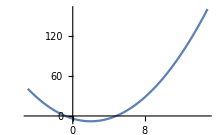

```mathematica
Plot[x^2-4*x-4,{x,-5,15}]
```

Kvadratická rovnica má 2 rôzne reálne korene => parabola pretína os x  v dvoch rôznych bodoch.

```mathematica
Solve[x^2-4x+4==0,x]//N
```

{{x→2.},{x→2.}}

```mathematica
Manipulate[Plot[x^2-4*x+4,{x,-5,15}]]
```

```mathematica
Solve[x^2-4x+14==0,x]//N
```

{{x→2.-3.16228 ⅈ},{x→2.+3.16228 ⅈ}}

```mathematica
Plot[x^2-4*x+14,{x,-5,15}]
```

-Graphics-

### Riešenie systémov rovníc

Na riešenie systémov rovníc Mathematica používa príkaz Solve. Základná štruktúra príkazu je rovnaká ako v prípade jednej rovnice, ale rovnice musia byť združené do skupiny (t.j. ohraničené množinovými zátvorkami)

Solve[ {rovnica_1, rovnica_2, ..., rovnica_k }, {neznáma_1,neznáma_2, ...,neznáma_k } ]		
		- presný výsledok 
Solve[  {rovnica_1, rovnica_2, ..., rovnica_k }, {neznáma_1,neznáma_2, ...,neznáma_k } ] //N		
		- presne vypočítané riešenie rovnice a následne je vyjadrená jeho numerická hodnota.

#### Príklad

Nájdite riešenie sústavy rovníc 
		x+2y=5
3x-4y=-2

Riešenie:

```mathematica
Solve[{x+2y==5,3x-4y==-2},{x,y}]
```

{{x→8/5,y→17/10}}

```mathematica
Solve[{x+2y==5,3x-4y==-2},{x,y}]//N
```

{{x→1.6,y→1.7}}

### Definícia funkcie

Veľmi často sa ocitáme v situácii, keď potrebujeme dlhšie pracovať s jednou funkciou - napr. potrebujeme vypočítať jej hodnotu v rôznych bodoch, nakresliť jej graf, nájsť jej priesečníky s osou x - ovou. Odvolávať sa na ňu len pomocou % je dosť nepohodlné. 
V takýchto situáciách je výhodnejšie funkciu zadefinovať. Čo to ale znamená "zadefinovať"? Znamená to vytvoriť "priečinok", pomenovať ho menom funkcie a do vnútra uložiť predpis, ktorým je táto funkcia definovaná. Štruktúra definície funkcie vyzerá nasledovne

		f[x_] = predpis

f je názov "priečinka", premenná x je nezávisle premenná, a "predpis" nám určuje funkciu. Podčiarovník ( _ ) za nezávisle premennou je veľmi dôležitý. On nám totiž zabezpečuje, že "priečinok" bude obsahovať funkciu, a nie len obyčajné priradenie. Prirodzenou sa zdá byť otázka, čo všetko môžeme získať definíciou funkcie. Okrem jednoduchšej manipulácie s funkciou, môžeme napr. veľmi jednoducho vypočítať jej hodnotu v ľubovoľnom bode (nielen v konkrétnom čísle), ako to ukazujú nasledujúce príklady.

```mathematica
f[x_]=(x+1)/(x-4)^2
```

(1+x)/(-4+x)^2

```mathematica
?f
```

```mathematica
f[3.5]
```

18.

```mathematica
(x+1)/(x-4)^2 /.x->3.5
```

18.

Všimnite si, že použitie definície funkcie je v istých situáciách ekvivalentom dosadzovacieho operátora. Pomocou definície funkcie ale jej hodnotu vypočítame jednoduchšie.

Funkciu definovanú predtým uvedeným predpisom môžeme veľmi jednoducho aj nakresliť. 
Všimnime si, že podčiarkovník sa použije len raz - v definícii funkcie.
Keď funkciu kreslíme, alebo pracujeme s jej argumentom, už podčiarkovník nepoužívame.

#### Príklad

Zadefinujte funkciu f: y = 4 e^(-x^2) .
	a)   Vypočítajte hodnotu funkcie v bode x=3.
	b)   Zobrazte graf f(x) na intervale x∈[-5,5].
	c)   Zobrazte graf f(x) na intervale x ∈ [-5, 5] a na celom jej obore hodnôt H(f).
	d)   Zobrazte graf f(x) na intervale x ∈ [-5, 5] a pre hodnoty y∈[0, 0.1].
	e)  Na grafe f(x) označte a pomenujte súradnicové osi x⃗  a y⃗.
	f)   Zobrazte graf  f(x) hrubšou čiarou.
	g)   Zobrazte graf  f(x) čiarkovanou čiarou.
	h)   Zobrazte graf  f(x) červenou čiarou
	i)   Zobrazte graf  f(x) červenou hrubou čiarou

Riešenie:

Začneme zadefinovaním funkcie f: y = 4 e^(-x^2) .

```mathematica
Clear[f,x]
f[x_]=4Exp[-x^2]
```

4 ⅇ^(-x^2)

Vypočítame hodnotu funkcie f(x) pre x=3.

```mathematica
f[3]
```

4/ⅇ^9

```mathematica
%//N
```

0.000493639

Zobrazte graf f(x) na intervale x∈[-5,5].

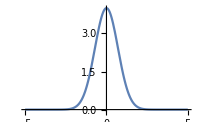

```mathematica
obr1=Plot[f[x],{x,-5,5}]
```

Zobrazte graf f(x) na intervale x ∈ [-5, 5] a na celom jej obore hodnôt H(f).

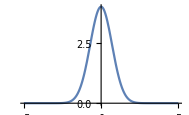

```mathematica
Plot[f[x],{x,-5,5},PlotRange->All]
```

Zobrazte graf f(x) na intervale x ∈ [-5, 5] a pre hodnoty y∈[0, 0.1].

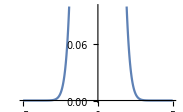

```mathematica
Plot[f[x],{x,-5,5},PlotRange->{0,0.1}]
```

Označenie súradnicových osí.

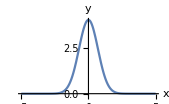

```mathematica
Plot[f[x],{x,-5,5},PlotRange->All,AxesLabel->{"x","y"}]
```

Zobrazte graf  f(x) hrubšou čiarou.

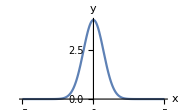

```mathematica
Plot[f[x],{x,-5,5},PlotRange->All,AxesLabel->{"x","y"},PlotStyle->Thick]
```

Zobrazte graf  f(x) čiarkovanou čiarou. Prvým parametrom (0.04) zadávame dĺžku čiarky, druhým parametrom (0.02) zadávame dĺžku medzery medzi čiarkami.

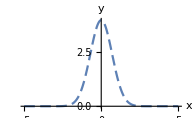

```mathematica
Plot[f[x],{x,-5,5},PlotRange->All,AxesLabel->{"x","y"},PlotStyle->Dashing[{0.04,0.02}]]
```

Zobrazte graf  f(x) červenou čiarou

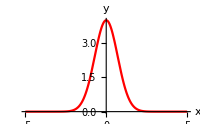

```mathematica
Plot[f[x],{x,-5,5},PlotRange->All,AxesLabel->{"x","y"},PlotStyle->Red]
```

Zobrazte graf  f(x) červenou hrubou čiarou

```mathematica
Plot[f[x],{x,-5,5},PlotRange->All,AxesLabel->{"x","y"},PlotStyle->{Red, Thick}]
```

-Graphics-

### Tabuľky

Posledná konštrukcia, ktorú si precvičíme na tomto cvičení je "tabuľka" (list, alebo pole, podľa toho, ako danú konštrukciu chápeme a ako s ňou budeme pracovať). Tento príkaz používame napríklad vtedy, ak potrebujeme vypočítať niekoľko hodnôt funkcie (chceme vytvoriť tabuľku hodnôt funkcie), alebo nakresliť niekoľko grafov funkcie pomocou jedného príkazu. Jej použitie je však omnoho bohatšie.

Jedna z možných štruktúr tohto príkazu je nasledovná

		Table[predpis, {parameter, od, do, krok]

#### Príklad

Vypíšte  tabuľku hodnôt x a  f(x)  ak f: y = log x+√(x+1) pre  x ∈[1,4] s krokom 0.5.  Tabuľku zobrazte s vhodným záhlavím.

```mathematica
Clear[f]
f[x_]=Log[x]+Sqrt[x+1];
tabulka=Table[{x,f[x]},{x,1,4,0.5}]
```

{{1.,1.41421},{1.5,1.9866},{2.,2.4252},{2.5,2.78712},{3.,3.09861},{3.5,3.37408},{4.,3.62236}}

```mathematica
TableForm[tabulka, TableHeadings->{None,{"x","Cell["f(x)",ExpressionUUID->"e2e09daa-dc6d-4107-a230-d8faa294193d"]"}}]
```

x | Cell["f(x)",ExpressionUUID->"e2e09daa-dc6d-4107-a230-d8faa294193d"]
1. | 1.41421
1.5 | 1.9866
2. | 2.4252
2.5 | 2.78712
3. | 3.09861
3.5 | 3.37408
4. | 3.62236

```mathematica
TableForm[tabulka, TableHeadings->{None,{"x","Cell["f(x)",ExpressionUUID->"f849472d-d034-498a-85e0-1bd2d770b065"]"}},TableSpacing->{1,4}]
```

x | Cell["f(x)",ExpressionUUID->"f849472d-d034-498a-85e0-1bd2d770b065"]
1. | 1.41421
1.5 | 1.9866
2. | 2.4252
2.5 | 2.78712
3. | 3.09861
3.5 | 3.37408
4. | 3.62236

```mathematica
TableForm[tabulka, TableHeadings->{Automatic,{"x","f(x)"}},TableSpacing->{1,4}]
```

| x | f(x)
1 | 1. | 1.41421
2 | 1.5 | 1.9866
3 | 2. | 2.4252
4 | 2.5 | 2.78712
5 | 3. | 3.09861
6 | 3.5 | 3.37408
7 | 4. | 3.62236

#### Zobrazenie grafu funkcie danej tabuľkou

Na zobrazenie grafu funkcie danej tabuľkou budeme používať príkaz 
		
		ListPlot[ {  {x_1,f(x_1)},{x_2,f(x_2)}, ...., {x_n,f(x_n)}   }] 

Tento príkaz zobrazí body so súradnicami {x_i,f(x_i)}  pre i=1,2,...n

Môžeme použiť aj grafické voľby pre nastavenie štýlu kreslenie:
	PlotStyle->{zoznam grafických direktív} 

Grafické direktívy:
	PointSize[r] - body sú vykreslené ako kruh s polomerom r
	RGBColor[červená, zelená, modrá]  - farba so špecifikovanými zložkami červená, zelená, modrá 
                               (každá môže byť z  [0,1],        0-neprítomnosť zložky, 1-prítomnosť zložky vo výslednej farbe)

Pomenovanie jednotlivých farieb

Red  ▪  Green  ▪  Blue  ▪  Black  ▪  White  ▪  Gray  ▪  Cyan  ▪  Magenta  ▪  Yellow  ▪  Brown  ▪  Orange  ▪  Pink  ▪  Purple

LightRed  ▪  LightGreen  ▪  LightBlue  ▪  LightGray  ▪  LightCyan  ▪  LightMagenta  ▪  LightYellow  ▪  
		LightBrown  ▪  LightOrange  ▪  LightPink  ▪  LightPurple

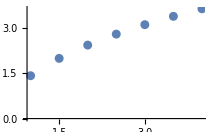

```mathematica
ListPlot[tabulka,PlotStyle->PointSize[0.03]]
```

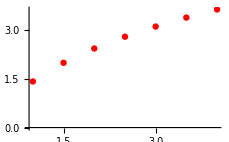

```mathematica
ListPlot[tabulka,PlotStyle->{PointSize[0.02],Red}]
```

```mathematica
paclet:ref/LightRed
```

```mathematica
paclet:ref/LightGreen
```

```mathematica
paclet:ref/LightBlue
```